# A Boolean model of geroconversion

Loading the library

```mathematica
$Path = $Path  ∪ {NotebookDirectory[]};
```

```mathematica
<<Booned`
```

```mathematica
Clear[TF, F, nodes, istates, states, nextstate, randomValues,n, simulation, ig0, sequential, parall,sg]
```

#### Transition function

```mathematica
TF = {
   Insulin -> Insulin,
   GF -> GF,
   Senescence ->  (! p16 && p21 && mTORC1S6K1) || (p16),
   G1S -> (! p21 && CDK2 && E2F1 && Metabolism),
   MAPK -> (GF && ! PP2A),
   p16 -> (MAPK && ! p53 && ! E2F1 && ! PRC),
   MDM2 -> (! p16 && ! p53 && AKT && ! mTORC1S6K1 && ! MYC && ! E2F1) || (! p16 && p53 && ! mTORC1S6K1 && ! MYC && ! E2F1) || (p16 && ! mTORC1S6K1 && ! MYC && ! E2F1),
   p53 -> (! MDM2),
   p21 -> (! p53 && ! AKT && ! MYC && FOXO) || (p53 && ! AKT && ! MYC),
   AKT -> (! IRSPIK3CA && ! PTEN && CDK2 && ! PP2A) || (IRSPIK3CA && ! PTEN && ! PP2A),
   mTORC1S6K1 -> (! AMPK && ! TSC),
   ATP -> Metabolism,
   IRSPIK3CA -> Insulin,
   AMPK -> (p53 && ! ATP),
   PTEN -> (p53 && ! AKT),
   TSC -> (! MAPK && ! AKT && AMPK),
   MYC -> (MAPK && ! p53 && mTORC1S6K1 && E2F1),
   CDK2 -> (! p21 && mTORC1S6K1 && ! MYC && E2F1) || (! p21 && mTORC1S6K1 && MYC),
   RB1 -> (! CDK2),
   E2F1 -> (! GF && MYC && ! RB1 && E2F1) || (GF && ! RB1 && E2F1),
   PRC -> (! AKT && MYC),
   Metabolism -> (! MAPK && ! AKT && mTORC1S6K1 && PP1C) || (! MAPK && AKT && mTORC1S6K1) || (MAPK && ! AKT && PP1C) || (MAPK && AKT),
   PP2A -> (! mTORC1S6K1),
   FOXO -> (! MAPK && ! p16 && ! AKT && ! AMPK && Metabolism) || (! MAPK && ! p16 && ! AKT && AMPK) || (! MAPK && p16 && ! AKT),
   PP1C -> (! MAPK && AKT) || (MAPK)
   };
```

#### List of rules

```mathematica
F = <|
   Insulin -> Insulin,
   GF -> GF,
   Senescence ->  (! p16 && p21 && mTORC1S6K1) || (p16),
   G1S -> (! p21 && CDK2 && E2F1 && Metabolism),
   MAPK -> (GF && ! PP2A),
   p16 -> (MAPK && ! p53 && ! E2F1 && ! PRC),
   MDM2 -> (! p16 && ! p53 && AKT && ! mTORC1S6K1 && ! MYC && ! E2F1) || (! p16 && p53 && ! mTORC1S6K1 && ! MYC && ! E2F1) || (p16 && ! mTORC1S6K1 && ! MYC && ! E2F1),
   p53 -> (! MDM2),
   p21 -> (! p53 && ! AKT && ! MYC && FOXO) || (p53 && ! AKT && ! MYC),
   AKT -> (! IRSPIK3CA && ! PTEN && CDK2 && ! PP2A) || (IRSPIK3CA && ! PTEN && ! PP2A),
   mTORC1S6K1 -> (! AMPK && ! TSC),
   ATP -> Metabolism,
   IRSPIK3CA -> Insulin,
   AMPK -> (p53 && ! ATP),
   PTEN -> (p53 && ! AKT),
   TSC -> (! MAPK && ! AKT && AMPK),
   MYC -> (MAPK && ! p53 && mTORC1S6K1 && E2F1),
   CDK2 -> (! p21 && mTORC1S6K1 && ! MYC && E2F1) || (! p21 && mTORC1S6K1 && MYC),
   RB1 -> (! CDK2),
   E2F1 -> (! GF && MYC && ! RB1 && E2F1) || (GF && ! RB1 && E2F1),
   PRC -> (! AKT && MYC),
   Metabolism -> (! MAPK && ! AKT && mTORC1S6K1 && PP1C) || (! MAPK && AKT && mTORC1S6K1) || (MAPK && ! AKT && PP1C) || (MAPK && AKT),
   PP2A -> (! mTORC1S6K1),
   FOXO -> (! MAPK && ! p16 && ! AKT && ! AMPK && Metabolism) || (! MAPK && ! p16 && ! AKT && AMPK) || (! MAPK && p16 && ! AKT),
   PP1C -> (! MAPK && AKT) || (MAPK)
   |>
```

<|Insulin→Insulin,GF→GF,Senescence→(!p16&&p21&&mTORC1S6K1)||p16,G1S→!p21&&CDK2&&E2F1&&Metabolism,MAPK→GF&&!PP2A,p16→MAPK&&!p53&&!E2F1&&!PRC,MDM2→(!p16&&!p53&&AKT&&!mTORC1S6K1&&!MYC&&!E2F1)||(!p16&&p53&&!mTORC1S6K1&&!MYC&&!E2F1)||(p16&&!mTORC1S6K1&&!MYC&&!E2F1),p53→!MDM2,p21→(!p53&&!AKT&&!MYC&&FOXO)||(p53&&!AKT&&!MYC),AKT→(!IRSPIK3CA&&!PTEN&&CDK2&&!PP2A)||(IRSPIK3CA&&!PTEN&&!PP2A),mTORC1S6K1→!AMPK&&!TSC,ATP→Metabolism,IRSPIK3CA→Insulin,AMPK→p53&&!ATP,PTEN→p53&&!AKT,TSC→!MAPK&&!AKT&&AMPK,MYC→MAPK&&!p53&&mTORC1S6K1&&E2F1,CDK2→(!p21&&mTORC1S6K1&&!MYC&&E2F1)||(!p21&&mTORC1S6K1&&MYC),RB1→!CDK2,E2F1→(!GF&&MYC&&!RB1&&E2F1)||(GF&&!RB1&&E2F1),PRC→!AKT&&MYC,Metabolism→(!MAPK&&!AKT&&mTORC1S6K1&&PP1C)||(!MAPK&&AKT&&mTORC1S6K1)||(MAPK&&!AKT&&PP1C)||(MAPK&&AKT),PP2A→!mTORC1S6K1,FOXO→(!MAPK&&!p16&&!AKT&&!AMPK&&Metabolism)||(!MAPK&&!p16&&!AKT&&AMPK)||(!MAPK&&p16&&!AKT),PP1C→(!MAPK&&AKT)||MAPK|>

```mathematica
Highlighted@TraditionalForm@TableForm[TF]
```

Insulin→Insulin
GF→GF
Senescence→(¬p16∧p21∧mTORC1S6K1)∨p16
G1S→¬p21∧CDK2∧E2F1∧Metabolism
MAPK→GF∧¬PP2A
p16→MAPK∧¬p53∧¬E2F1∧¬PRC
MDM2→(¬p16∧¬p53∧AKT∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(¬p16∧p53∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(p16∧¬mTORC1S6K1∧¬MYC∧¬E2F1)
p53→¬MDM2
p21→(¬p53∧¬AKT∧¬MYC∧FOXO)∨(p53∧¬AKT∧¬MYC)
AKT→(¬IRSPIK3CA∧¬PTEN∧CDK2∧¬PP2A)∨(IRSPIK3CA∧¬PTEN∧¬PP2A)
mTORC1S6K1→¬AMPK∧¬TSC
ATP→Metabolism
IRSPIK3CA→Insulin
AMPK→p53∧¬ATP
PTEN→p53∧¬AKT
TSC→¬MAPK∧¬AKT∧AMPK
MYC→MAPK∧¬p53∧mTORC1S6K1∧E2F1
CDK2→(¬p21∧mTORC1S6K1∧¬MYC∧E2F1)∨(¬p21∧mTORC1S6K1∧MYC)
RB1→¬CDK2
E2F1→(¬GF∧MYC∧¬RB1∧E2F1)∨(GF∧¬RB1∧E2F1)
PRC→¬AKT∧MYC
Metabolism→(¬MAPK∧¬AKT∧mTORC1S6K1∧PP1C)∨(¬MAPK∧AKT∧mTORC1S6K1)∨(MAPK∧¬AKT∧PP1C)∨(MAPK∧AKT)
PP2A→¬mTORC1S6K1
FOXO→(¬MAPK∧¬p16∧¬AKT∧¬AMPK∧Metabolism)∨(¬MAPK∧¬p16∧¬AKT∧AMPK)∨(¬MAPK∧p16∧¬AKT)
PP1C→(¬MAPK∧AKT)∨MAPK

#### Set the initial states randomly (p=0.5 for each node)

```mathematica
nodes = {Insulin,GF, Senescence, G1S,MAPK, p16,MDM2,p53,p21,AKT,mTORC1S6K1, ATP, IRSPIK3CA, AMPK, PTEN,TSC, MYC, CDK2,RB1, E2F1,PRC, Metabolism,PP2A, FOXO, PP1C}
```

{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}

```mathematica
randomValues=RandomChoice[{True,False},Length[nodes]]
```

{True,True,False,False,True,False,True,False,False,True,True,True,True,False,False,True,False,True,False,False,True,False,True,False,False}

```mathematica
states=<|Thread[nodes->randomValues]|>
```

<|Insulin→True,GF→True,Senescence→False,G1S→False,MAPK→True,p16→False,MDM2→True,p53→False,p21→False,AKT→True,mTORC1S6K1→True,ATP→True,IRSPIK3CA→True,AMPK→False,PTEN→False,TSC→True,MYC→False,CDK2→True,RB1→False,E2F1→False,PRC→True,Metabolism→False,PP2A→True,FOXO→False,PP1C→False|>

```mathematica
nextstate = F/.states
```

<|Insulin→True,GF→True,Senescence→(!False&&False&&True)||False,G1S→!False&&True&&False&&False,MAPK→True&&!True,p16→True&&!False&&!False&&!True,MDM2→(!False&&!False&&True&&!True&&!False&&!False)||(!False&&False&&!True&&!False&&!False)||(False&&!True&&!False&&!False),p53→!True,p21→(!False&&!True&&!False&&False)||(False&&!True&&!False),AKT→(!True&&!False&&True&&!True)||(True&&!False&&!True),mTORC1S6K1→!False&&!True,ATP→False,IRSPIK3CA→True,AMPK→False&&!True,PTEN→False&&!True,TSC→!True&&!True&&False,MYC→True&&!False&&True&&False,CDK2→(!False&&True&&!False&&False)||(!False&&True&&False),RB1→!True,E2F1→(!True&&False&&!False&&False)||(True&&!False&&False),PRC→!True&&False,Metabolism→(!True&&!True&&True&&False)||(!True&&True&&True)||(True&&!True&&False)||(True&&True),PP2A→!True,FOXO→(!True&&!False&&!True&&!False&&False)||(!True&&!False&&!True&&False)||(!True&&False&&!True),PP1C→(!True&&True)||True|>

```mathematica
Evaluate/@nextstate
```

<|Insulin→True,GF→True,Senescence→False,G1S→False,MAPK→False,p16→False,MDM2→False,p53→False,p21→False,AKT→False,mTORC1S6K1→False,ATP→False,IRSPIK3CA→True,AMPK→False,PTEN→False,TSC→False,MYC→False,CDK2→False,RB1→False,E2F1→False,PRC→False,Metabolism→True,PP2A→False,FOXO→False,PP1C→True|>

```mathematica
Boole [nextstate]
```

<|Insulin→1,GF→1,Senescence→0,G1S→0,MAPK→0,p16→0,MDM2→0,p53→0,p21→0,AKT→0,mTORC1S6K1→0,ATP→0,IRSPIK3CA→1,AMPK→0,PTEN→0,TSC→0,MYC→0,CDK2→0,RB1→0,E2F1→0,PRC→0,Metabolism→1,PP2A→0,FOXO→0,PP1C→1|>

#### Step computation function

```mathematica
Step[states_]:=F/. states
```

#### Simulation

```mathematica
n = 10
```

10

```mathematica
simulation=NestList[Step,states,n];
```

#### Visualisation

```mathematica
TableForm[Boole[Values@simulation]/. {0->Style[0,Red,Bold],1->Style[1,Blue,Bold]},TableHeadings->{Range[0,n],Keys[F]}]
```

| Insulin | GF | Senescence | G1S | MAPK | p16 | MDM2 | p53 | p21 | AKT | mTORC1S6K1 | ATP | IRSPIK3CA | AMPK | PTEN | TSC | MYC | CDK2 | RB1 | E2F1 | PRC | Metabolism | PP2A | FOXO | PP1C
0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
2 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
3 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
4 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
5 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
6 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
7 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
8 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
9 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
10 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1

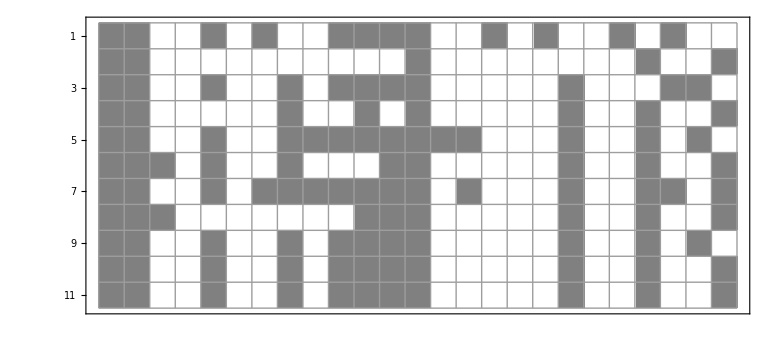

```mathematica
ArrayPlot[Values[simulation],ColorRules->{True->Gray,False->White},Mesh->True,Frame->True,FrameTicks->{{Range[1,n+1],None},{None,Thread[{Range@Length[F],Keys[F]}]}}]
```

The set of variables of the Boolean network.

```mathematica
Keys[TF]
```

{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}

#### Interaction graph

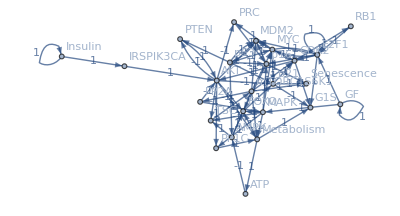

```mathematica
ig0 = InteractionGraphSimple[TF]
```

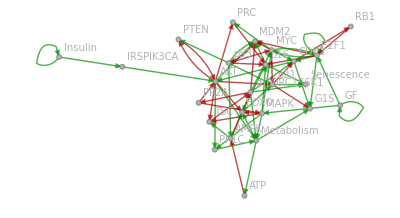

```mathematica
NiceIG[ig0]
```

```mathematica
NiceIG3D[ig0]
```

-Graphics3D-

#### Regulators

```mathematica
Regulators[ig0, mTORC1S6K1, {-1,0,1}]
```

{AMPK,TSC}

```mathematica
Regulators[ig0, Senescence, {-1,1}]
```

{mTORC1S6K1,p16,p21}

```mathematica
Regulators[ig0, G1S, {-1}]
```

{p21}

```mathematica
Regulators[ig0, G1S, {1}]
```

{CDK2,E2F1,Metabolism}

#### State graph computation

The state graph of a Boolean network serves to illustrate the dynamic behavior of the network over time. It provides a graphical representation of the possible states the network can transition through as it evolves according to its Boolean rules.

The computation of a model (state graph)  depends on the modalities. Two modalities are predefined

Sequential and Parallel modes.

```mathematica
sequential=Sequential@Keys[TF]
```

{{Insulin},{GF},{Senescence},{G1S},{MAPK},{p16},{MDM2},{p53},{p21},{AKT},{mTORC1S6K1},{ATP},{IRSPIK3CA},{AMPK},{PTEN},{TSC},{MYC},{CDK2},{RB1},{E2F1},{PRC},{Metabolism},{PP2A},{FOXO},{PP1C}}

```mathematica
parall=Parallel@Keys[TF]
```

{{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}}

```mathematica
sg= ModelOf[TF]
```

ModelOf[TF]